## Parametri e Variabili:

```mathematica
ClearAll;
Nspin=10000; (*Numero di spin*)
(*Numero di iterazioni e passo iterativo*)
Niter=50000;
dt=0.005;
beta = 1.25;
alfa = 2; (* parametro gamma*)
gamma = 0.1; (* è il beta di una gamma(alfa,beta)*)
sigma = 1; (* serve per la inverse gamma *)
k = 2;
eps = 0.05;


F[y_] = PDF[GammaDistribution[alfa,gamma],y]/(1-CDF[GammaDistribution[alfa,gamma],y]);
G[y_] = PDF[InverseGammaDistribution[1/2,1/(2*(sigma^2))],y]/(1-CDF[InverseGammaDistribution[1/2,1/(2*(sigma^2))],y]);   (*Inverse gamma con formula hitting time moto browniano*)

H[y_] = PDF[ErlangDistribution[alfa,gamma],y]/(1-CDF[ErlangDistribution[alfa,gamma],y]);

P[y_] = y;

(*N[F[0],5]*)
(*F[Exp[-beta*X[[j]]*MediaEmperica[[i]]]* Y[[j]]] *Exp[-beta*X[[j]]*MediaEmperica[[i]]]*dt*)
(* caso gamma distributed *)
(*Exp[-beta*X[[j]]*MediaEmperica[[i]]]*dt*) (* caso esponenziale *)
```

## Condizioni iniziali:

```mathematica
(*X=Table[1,{iy,1,Nspin}]; (* spin tutti in 1*)*)
X= Join[Table[RandomChoice[{-1,1}],{iy,1,Nspin}]];(*Table[-1,{it,1,Nspin/2  - 100}]];*)(*media iniz nulla*)
Y =Table[RandomReal[],{iy,1,Nspin}]; (* i clocks *)
MediaEmperica=Table[0,{it,1,Niter}];
SommaY = Table[0,{it,1,Niter}];
SommaXY = Table[0,{it,1,Niter}];
T = Table[{0,0},{it,1,Niter}];
S = Table[{0,0},{it,1,Niter}];
Total[X]/Nspin
```

-7/5000

## Simulazioni Sistema Stocastico:

```mathematica
For[i=1,i≤Niter-1, i++,
MediaEmperica[[i]]=N[Total[X]/Nspin];
SommaY[[i]] = N[Total[Y]/Nspin];
SommaXY[[i]] = N[Total[X*Y]/Nspin];
T[[i]] = {MediaEmperica[[i]],SommaXY[[i]]};
S[[i]] = {MediaEmperica[[i]], SommaY[[i]]};
Y=Y + dt;
For[j=1,j≤Nspin,j++,
z=RandomReal[];
If[z<P[Exp[-beta*X[[j]]*MediaEmperica[[i]]]*Y[[j]]]*Exp[-beta*X[[j]]*MediaEmperica[[i]]]*dt, 
Y[[j]]=0;
X[[j]]=-X[[j]];
];
];
];
```

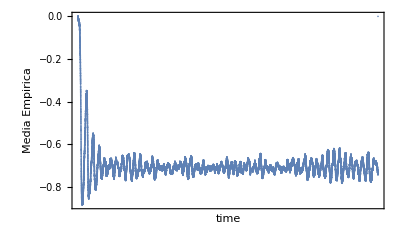

```mathematica
(*Bound1=Table[a+ϵ,{ix1,1,Niter}];
Bound2=Table[-a-ϵ,{ix1,1,Niter}];*)
A=ListPlot[MediaEmperica,Frame->True,Axes->False,FrameLabel->{"time","Media Empirica"},FrameTicksStyle->Directive[12,Black],LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,None},{None,None}},PlotRange->{All,All}]
```

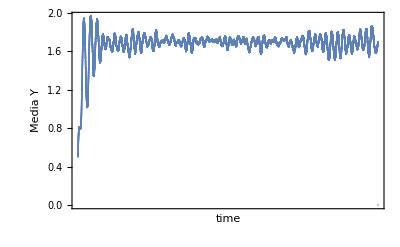

```mathematica
B=ListPlot[SommaY,Frame->True,Axes->False,FrameLabel->{"time","Media Y"},FrameTicksStyle->Directive[12,Black],LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,None},{None,None}},PlotRange->{All,All}]
```

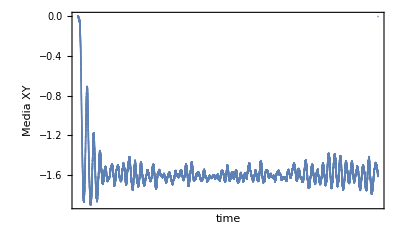

```mathematica
J=ListPlot[SommaXY,Frame->True,Axes->False,FrameLabel->{"time","Media XY"},FrameTicksStyle->Directive[12,Black],LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,None},{None,None}},PlotRange->{All,All}]
```

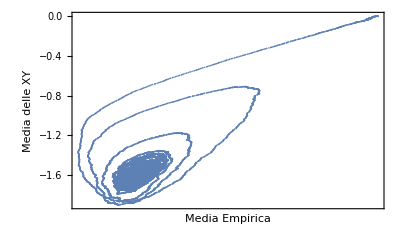

```mathematica
M = ListPlot[T,Frame->True,Axes->False,FrameLabel->{"Media Empirica","Media delle XY"},FrameTicksStyle->Directive[12,Black],LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,None},{None,None}},PlotRange->{All,All}]
```

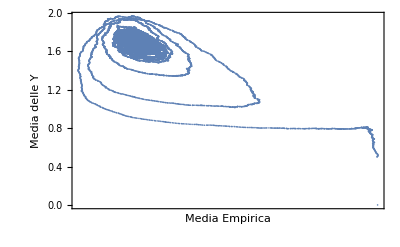

```mathematica
G= ListPlot[S,Frame->True,Axes->False,FrameLabel->{"Media Empirica","Media delle Y"},FrameTicksStyle->Directive[12,Black],LabelStyle->Directive[Black,16],FrameTicks->{{Automatic,None},{None,None}},PlotRange->{All,All}]
```

```mathematica
Export["/Users/guglielmo/Desktop/semimarkov/gamma=1_sim_Nparticles/media_emp_b=1.25.jpg",A];

Export["/Users/guglielmo/Desktop/semimarkov/gamma=1_sim_Nparticles/media_Y_b=1.25.jpg",B];

Export["/Users/guglielmo/Desktop/semimarkov/gamma=1_sim_Nparticles/media_XY_b=1.25.jpg",J];

Export["/Users/guglielmo/Desktop/semimarkov/gamma=1_sim_Nparticles/media_XY_vs_emp_b=1.25.jpg",M];
Export["/Users/guglielmo/Desktop/semimarkov/gamma=1_sim_Nparticles/media_Y_vs_emp_b=1.25.jpg",G];
```